```mathematica
PiRectangles[n_]:=Module[{pi,pts,i},
pts=Table[0,{i,0,n}];
pi=RealDigits[Pi,10,n];
pi=pi[[1]];
For[i=1,i≤n,i++,
pts[[i+1]]=pts[[i]]+Floor[pi]*Exp[i*ⅈ*Pi/2];
pi=10Mod[pi,1];
Print[pi];
];
pts=Table[{Re[pts[[i]]],Im[pts[[i]]]},{i,1,n+1}];
Show[Graphics[Line[pts]]]
];
```

1.41593

4.15927

1.59265

5.92654

9.26536

2.65359

6.5359

5.35898

3.58979

5.89793

8.97931

9.79312

7.93116

9.3116

3.116

1.15998

1.5998

5.99796

9.97963

9.79635

7.96347

9.63469

6.34685

3.46854

4.68544

6.85442

8.54419

5.44185

4.41852

4.18516

1.85162

8.51616

5.16159

1.61591

6.15906

1.59058

5.90576

9.05762

0.576172

5.76172

7.61719

6.17188

1.71875

7.1875

1.875

8.75

7.5

5.

0.

0.

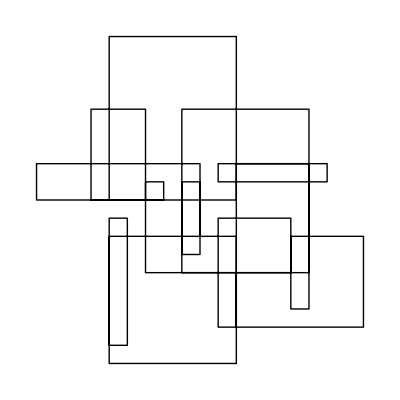

```mathematica
PiRectangles[50]
```

```mathematica
Pi*1.
```

3.14159

```mathematica
RealDigits[Pi,10,100]
```

{{3,1,4,1,5,9,2,6,5,3,5,8,9,7,9,3,2,3,8,4,6,2,6,4,3,3,8,3,2,7,9,5,0,2,8,8,4,1,9,7,1,6,9,3,9,9,3,7,5,1,0,5,8,2,0,9,7,4,9,4,4,5,9,2,3,0,7,8,1,6,4,0,6,2,8,6,2,0,8,9,9,8,6,2,8,0,3,4,8,2,5,3,4,2,1,1,7,0,6,7},1}